```mathematica
SetDirectory["/home/meike/Documents/"];
Get["PlotTheme.m"]
$PlotTheme="Publication";
Needs["ErrorBarPlots`"];
SetDirectory[]; 
path="/home/meike/Documents/literature/conferences/Elisbon/day07/exercise3/";
```

```mathematica
settings=Import[path<>"run01/settings.dat"]
tmax=settings[[1,2]];
dt=settings[[2,2]];
Ngrid=settings[[3,2]];
tprint=settings[[4,2]];
```

{{tmax,100},{dt,0.01},{N,100},{tprint,1},{lambda,0.1},{Pe,3.16228}}

```mathematica
tplus=IntegerPart[tprint/dt]
tmaxsteps=IntegerPart[tmax/dt]
gridt={};

For[t = 0, t <tmaxsteps, t+=100, 
grid=Import[path<>"run02/grid_t"<>ToString[t]<>".dat"];
AppendTo[gridt,grid];
]
```

1000

100000

Import::nffil: File /home/meike/Documents/literature/conferences/Elisbon/day07/exercise3/run02/grid_t100.dat not found during Import.

Import::nffil: File /home/meike/Documents/literature/conferences/Elisbon/day07/exercise3/run02/grid_t200.dat not found during Import.

Import::nffil: File /home/meike/Documents/literature/conferences/Elisbon/day07/exercise3/run02/grid_t300.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
Max[gridt[[1]]]
```

0.999211

```mathematica
Manipulate[ListDensityPlot[gridt[[step]],ColorFunction->ColorData[{"RedBlueTones",{0,1}}],ColorFunctionScaling->False,PlotLegends->Automatic],{step,1,Length[gridt],1}]
```

Part::partd: Part specification gridt⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: gridt⟦1⟧ must be a valid array.

Part::partd: Part specification gridt⟦1⟧ is longer than depth of object.

ListDensityPlot::arrayerr: gridt⟦1⟧ must be a valid array.

Part::partw: Part 20 of {} does not exist.

ListDensityPlot::arrayerr: {}⟦20⟧ must be a valid array.

Part::partw: Part 20 of {} does not exist.

ListDensityPlot::arrayerr: {}⟦20⟧ must be a valid array.

Part::partw: Part 8 of {} does not exist.

ListDensityPlot::arrayerr: {}⟦8⟧ must be a valid array.

ListDensityPlot::arrayerr: $Failed must be a valid array.

```mathematica
StreamPlot[{0.5*Cos[x]*Sin[y],0.5*Sin[x]*Cos[y]},{x,0,2π},{y,0,2π}];
```

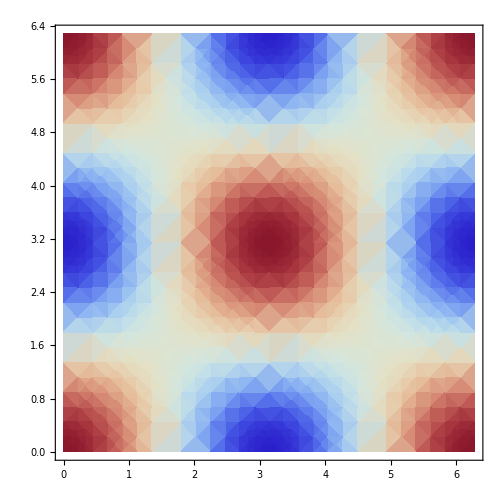

```mathematica
DensityPlot[2Cos[x]Cos[y],{x,0,2π},{y,0,2π}]
```

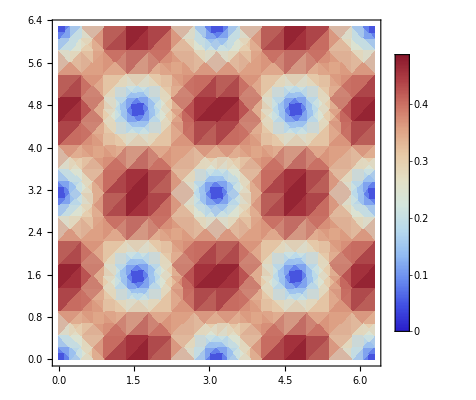

```mathematica
DensityPlot[Norm[{0.5*Cos[x]*Sin[y],0.5*Sin[x]*Cos[y]}],{x,0,2π},{y,0,2π},PlotLegends->Automatic]
```

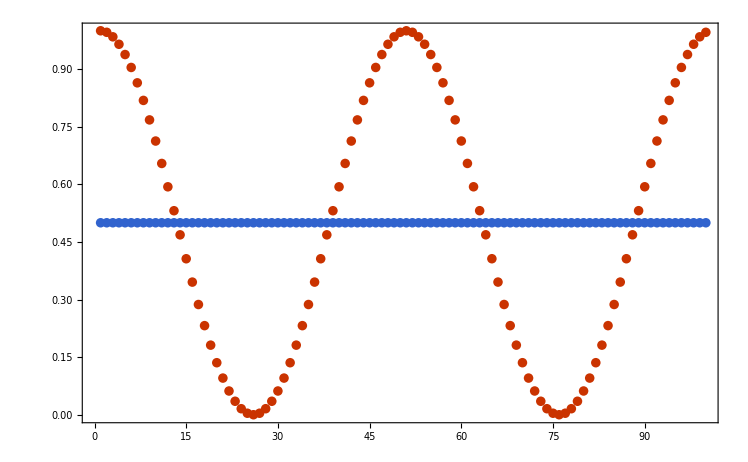

```mathematica
ListPlot[{gridt[[1,All,10]],gridt[[-1,All,10]]}]
```

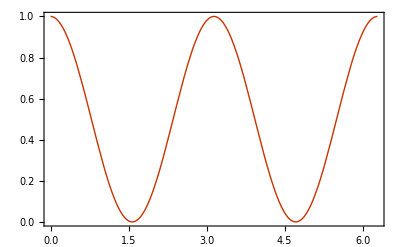

```mathematica
Plot[Cos[x]^2,{x,0,2π}]
```

```mathematica
Remove[t,c]
```

```mathematica
DSolve[{D[c[t,x,y],t]+0.5*Cos[x]*Sin[y]*D[c[t,x,y],x]+0.5*Sin[x]*Cos[y]*D[c[t,x,y],y]==D[c[t,x,y],x]+D[c[t,x,y],y],c[0,x,y]==Cos[x]^2},c[t,x,y],{t}]
```

{{c[t,x,y]→Cos[x]^2+(1.+0. ⅈ) ((0.+0. ⅈ)+(1.+0. ⅈ) c^(0,0,1)[K[1],x,y]-(0.25+0. ⅈ) Sin[x-1. y] c^(0,0,1)[K[1],x,y]-(0.25+0. ⅈ) Sin[x+y] c^(0,0,1)[K[1],x,y]+(1.+0. ⅈ) c^(0,1,0)[K[1],x,y]+(0.25+0. ⅈ) Sin[x-1. y] c^(0,1,0)[K[1],x,y]-(0.25+0. ⅈ) Sin[x+y] c^(0,1,0)[K[1],x,y])K[1]0t}}